Reaching supercritical field strengths with intense lasers

T G Blackburn et al 2019 New J. Phys. 21 053040
Notebook: Óscar Amaro, Feb 2022 @ GoLP-EPP

Attention: There is either a flawed implementation of neff or χmax (compare with all figures from the paper), and with this implementation the 50 GeV in Figure 4 are not consistent with the paper.

Physical constants

```mathematica
(*α fine structure constant*)
α = 1/137; (*[#]*)
(*c speed of light in vacuum*)
c = 299792458; (*[m/s]*)
(*m electron mass*)
m = 0.5109989461/1000; (*[GeV]*)
(*ℏ Planck's constant*)
ℏ = 6.626070040*10^-34 /(2π);
(*e electron abs charge*)
e = 1.6021766208*10^-19;
```

```mathematica
Clear[g,χc,χmax,δ,eq5a,Rcneff,W]

(*Gaunt factor*)
g[χ_]:=(1+4.8(1+χ)Log[1+1.7χ]+2.44χ^2)^(-2/3)
(*(8) critical χc*)
χc[γ0_,a0_,ω0_,n_]:=FindRoot[χ^4g[χ]^2-(72N[Log[2]])/(π^2 α^2)((γ0 ω0)/(n m))^2Log[(2 γ0 a0 ω0)/(m χ)],{χ,10^-10}][[1,2]]
(*(4) χmax, here χ=χ/χ0*)
χmax[Rcneff_,θ_,mm_]:=FindRoot[χ^4g[χ mm]^2-(9Log[2](1+Cos[θ])^2)/(π Rcneff)^2 Log[(1+Cos[θ])/(2χ)],{χ,10^-10}][[1,2]]
(*(5b)*)
δ[θ_,Rcneff_]:=(π Rcneff (1+Cos[θ]))/(3Sqrt[2Log[2]])
(*(5a)*)
eq5a[θ_,Rcneff_]:=(1+Cos[θ])/2 Exp[-W[δ[θ,Rcneff]^2]/5]
(* Lambert function W*)
W[x_]:=ProductLog[x]
```

Figure 1
Analytical prediction of χmax of electron

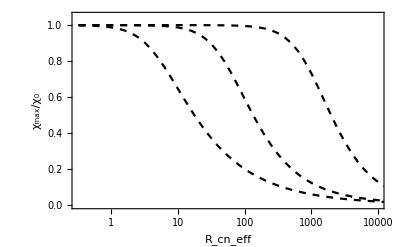

```mathematica
(*FIG.1.*)
(*Gaunt factor*)
g[χ_]:=(1+4.8(1+χ)Log[1+1.7χ]+2.44χ^2)^(-2/3)
(*(4) χmax, here χ=χ/χ0*)
χmax[Rcneff_,θ_,mm_]:=FindRoot[χ^4g[χ mm]^2-(9Log[2](1+Cos[θ])^2)/(π Rcneff)^2 Log[(1+Cos[θ])/(2χ)],{χ,10^-10}][[1,2]]
Rcneff=ParallelTable[10^i,{i,-0.7,4.5,0.1}];
χ0={1,10,100};
χmaxx=ParallelTable[{Rcneff[[i]],χmax[Rcneff[[i]],0,χ0[[j]]]},{i,1,Length[Rcneff]},{j,1,Length[χ0]}];
fig1=ListLogLinearPlot[{χmaxx[[All,1]],χmaxx[[All,2]],χmaxx[[All,3]]},Joined->True,Axes->False,PlotStyle->Directive[Dashed,Black,15],PlotRange->{{10^-0.5,10^4},{0,1.05}},Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"R_cn_eff","χ_max/χ_0"}];
fig1
```

Figure 2
Angle at which χmax is largest

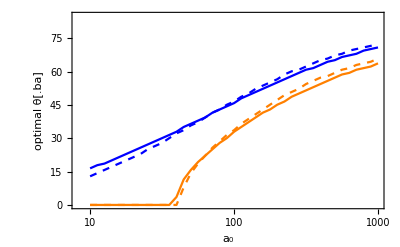

```mathematica
Clear[a0,γ0,λ,ω0,ω0m,dθ,χ0,Rc,χmax,χ0,da0]

λ=0.8;(*μm*)
r0=2 ;(*μm*)
ω0=2π c/(λ/10^6);
ω0m=2π c/(λ/10^6) ℏ/e/10^9;

(*Gaunt factor*)
g[χ_]:=(1+4.8(1+χ)Log[1+1.7χ]+2.44χ^2)^(-2/3)
(*(3) neff *)
neff[θ_,τ_]:=(ω0 τ 10^-6 / c)/(2π)(1+τ^2/r0^2 Tan[θ/2]^2/Log[4])^(-1/2)
(*(4) find χmax*)
χmax[a0_,θ_,γ0_,τ_]:=FindRoot[χ^4g[χ]^2/(2 a0 γ0 ω0m/m)^4  -(9Log[2](1+Cos[θ])^2)/(π α a0 2a0 γ0 ω0m/m   neff[θ,τ])^2 Log[((1+Cos[θ])(2a0 γ0 ω0m/m))/(2χ)],{χ,10^-7}][[1,2]]//Quiet
(*χ0 is χe at θ=0, χ0=2 a0 γ0 ω0/m;*)
(*Rc=α a0 χ0*)

optθ[a0_,γ0_,τ_]:=Module[{tab,dθ},
dθ=0.1/4/2;
tab=Table[{θ,χmax[a0,θ,γ0,τ]},{θ,0,π/2,dθ}];
Return[tab[[Position[tab[[All,2]],Max[tab[[All,2]]]][[1,1]],1]]];
]

(* create tables*)
da0=0.1/2;
tab50full=Table[{10^a0,optθ[10^a0,2 10^4,50 λ] 180/π},{a0,Log10[10],Log10[1000],da0}];
tab50dash=Table[{10^a0,optθ[10^a0,5 10^3,50 λ] 180/π},{a0,Log10[10],Log10[1000],da0}];
tab10full=Table[{10^a0,optθ[10^a0,2 10^4,10 λ] 180/π},{a0,Log10[10],Log10[1000],da0}];
tab10dash=Table[{10^a0,optθ[10^a0,5 10^3,10 λ] 180/π},{a0,Log10[10],Log10[1000],da0}];

(*Plot*)
ListLogLinearPlot[{tab50full,tab50dash,tab10full,tab10dash},Joined->True,PlotStyle->{Directive[Blue],Directive[Blue,Dashed],Directive[Orange],Directive[Orange,Dashed]},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"a_0","optimal θ[.ba]"},PlotRange->{0,85}]
```

Figure 3
Enhanced quantum effects at oblique incidence

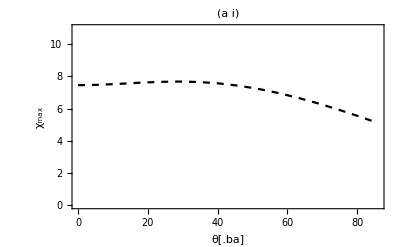

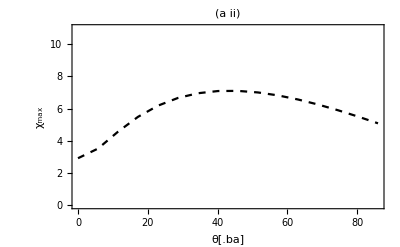

```mathematica
Clear[a0,γ0,λ,ω0,ω0m,dθ,χ0,Rc,χmax,χ0,da0]

λ=0.8;(*[μm]*)
r0=2 ;(*[μm]*)
a0=82.4;(*[]*)
ω0=2π c/(λ/10^6);
ω0m=2π c/(λ/10^6) ℏ/e/10^9;

(*Gaunt factor*)
g[χ_]:=(1+4.8(1+χ)Log[1+1.7χ]+2.44χ^2)^(-2/3)
(*(3) neff *)
neff[θ_,τ_]:=(ω0 τ 10^-6 / c)/(2π)(1+τ^2/r0^2 Tan[θ/2]^2/Log[4])^(-1/2)
(*(4) find χmax*)
χmax[a0_,θ_,γ0_,τ_]:=FindRoot[χ^4g[χ]^2/(2 a0 γ0 ω0m/m)^4  -(9Log[2](1+Cos[θ])^2)/(π α a0 2a0 γ0 ω0m/m   neff[θ,τ])^2 Log[((1+Cos[θ])(2 a0 γ0 ω0m/m))/(2χ)],{χ,10^-7}][[1,2]]//Quiet
(*tables*)
tab1=Table[{180/π θ,χmax[a0,θ,2 10^4,10λ]},{θ,0,π/2,0.1}];
tab2=Table[{180/π θ,χmax[a0,θ,2 10^4,50λ]},{θ,0,π/2,0.1}];
(*plot*)
ListPlot[tab1,Joined->True,PlotStyle->Directive[Dashed,Black],PlotRange->{0,11},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"θ[.ba]","χ_max"},PlotLabel->"(a i)"]
ListPlot[tab2,Joined->True,PlotStyle->Directive[Dashed,Black],PlotRange->{0,11},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"θ[.ba]","χ_max"},PlotLabel->"(a ii)"]
```

Figure 4
Minimum γ0 and a0 required for χe>=100

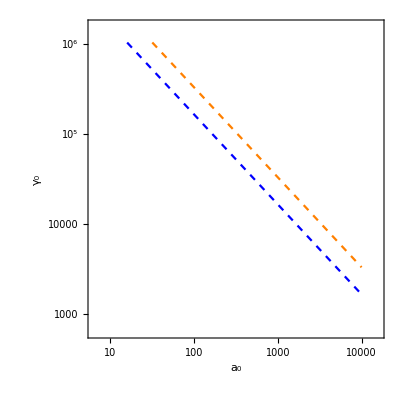

```mathematica
(*FIG.4.*)
Clear[λ,ω0,γ0min,p1,p2]
λ=0.8;
ω0=2π c/(λ/10^6) ℏ/e/10^9;
γ0min[a0_,χe_,θ_]:=(m χe)/(a0 ω0 (1+Cos[θ]))
p1=LogLogPlot[γ0min[a0,100,0],{a0,10^1.2,10^4},Axes->False,PlotStyle->Directive[Dashed,Blue,15],PlotRange->{{10^0.8,10^4.2},{10^2.8,10^6.2}},Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"a_0","γ_0"},AspectRatio->1];
p2=LogLogPlot[γ0min[a0,100,π/2],{a0,10^1.5,10^4},Axes->False,PlotStyle->Directive[Dashed,Orange,15],PlotRange->{{10^0.8,10^4.2},{10^2.8,10^6.2}},Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"a_0","γ_0"},AspectRatio->1];
Show[p1,p2]
```

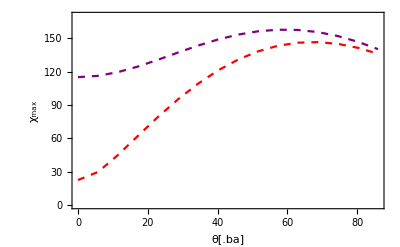

```mathematica
Clear[a0,γ0,λ,ω0,ω0m,dθ,χ0,Rc,χmax,χ0,da0]

λ=0.8;(*[μm]*)
r0=2 ;(*[μm]*)
a0=1000;(*[]*)
ω0=2π c/(λ/10^6);
ω0m=2π c/(λ/10^6) ℏ/e/10^9;

(*Gaunt factor*)
g[χ_]:=(1+4.8(1+χ)Log[1+1.7χ]+2.44χ^2)^(-2/3)
(*(3) neff *)
neff[θ_,τ_]:=(ω0 τ 10^-6 / c)/(2π)(1+τ^2/r0^2 Tan[θ/2]^2/Log[4])^(-1/2)
(*(4) find χmax*)
χmax[a0_,θ_,γ0_,τ_]:=FindRoot[χ^4g[χ]^2/(2 a0 γ0 ω0m/m)^4  -(9Log[2](1+Cos[θ])^2)/(π α a0 2a0 γ0 ω0m/m   neff[θ,τ])^2 Log[((1+Cos[θ])(2 a0 γ0 ω0m/m))/(2χ)],{χ,10^-7}][[1,2]]//Quiet
(*inset plot*)
plt1=ListPlot[Table[{180/π θ,χmax[a0,θ,40/m,10λ]},{θ,0,π/2,0.1}],Joined->True,PlotStyle->Directive[Dashed,Purple],PlotRange->{0,170},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"θ[.ba]","χ_max"}];
plt2=ListPlot[Table[{180/π θ,χmax[a0,θ,40/m,50λ]},{θ,0,π/2,0.1}],Joined->True,PlotStyle->Directive[Dashed,Red],PlotRange->{0,170},Axes->False,Frame->True,FrameStyle->Directive[Black,15],FrameLabel->{"θ[.ba]","χ_max"}];
Show[{plt1,plt2}]
```